# MATH&254 Project 4: Driving in the Rain

Names
• Leigh Cox
• Kristina Ilyovska
• Thu Luu
• Bob Schmitz

Instructions
This is due Friday, Dec. 7, at 11:59pm.
Email me a Mathematica notebook with your completed project by the due date.
Please number the problems in your solutions. If you are asked to compute or plot something, put the
problem number in a section cell or text cell above your code. If you are asked to explain something, do it
in a text cell.

## Introduction

An age-old question in mathematics (and physics) is whether it is better to run or walk in the rain. If you
walk, you don’t get as much rain hitting your front (it just hits your head and shoulders) but you are in the
rain for a longer time. If you run, some rain hits your front, but you are rained on for a shorter time. In
this project you will compute some flux integrals to quantify this situation.
People are very irregularly shaped, so instead we’ll model the windshield of a car. Throughout the project,
x, y, and z will be measured in meters.

## The Windshield

We’ll model the windshield of a car with a portion of the ellipsoid

x^2/0.8^2+y^2/3^2+z^2=1

1. Find a parametrization of the ellipsoid, can call it r[u_,v_]. Then use ParametricPlot3D[ ] to plot
the entire ellipsoid. The best way to do this is to start with the parametrization of a sphere of radius ρ (which comes from
spherical coordinates, treating ρ as a constant), where u represents θ and v represents φ, then using
different radii in each of the three components.

For our windshield, we’ll only use the portion where u (the angle in the xy-plane) is in [−0.3, 0.3] and
v (the angle from the positive z axis) is in [0.9, π/2]. This should look like a slightly bent rectangle,
which about 2 meters long in the y-direction and 0.6 meters tall in the z-direction.

```mathematica
r[θ_,ϕ_]:={0.8Sin[ϕ]Cos[θ],3Sin[ϕ]Sin[θ],Cos[ϕ]}
```

```mathematica
ParametricPlot3D[r[θ,ϕ],{θ,0,2π},{ϕ,0,π}]
```

-Graphics3D-

```mathematica
surface=ParametricPlot3D[r[θ,ϕ],{θ,-.3,.3},{ϕ,.9,π/2}]
```

-Graphics3D-

2. Plot the portion of the ellipsoid described above, and compute an integral to find its surface area. I
suggest you use NIntegrate[ ] to speed up the calculation. You should get about 1.08 m^2

```mathematica
rθ:=D[r[θ,ϕ],θ]
rϕ:=D[r[θ,ϕ],ϕ]
rθxrϕ:=Cross[rθ,rϕ]
```

```mathematica
NIntegrate[Norm[rθxrϕ],{θ,-.3,.3},{ϕ,.9,π/2}]
```

1.0786

## The Rain

Let’s assume the rain is coming straight down at 10 m/s, so that if we’re not driving, the rain is modeled
by the vector field

```mathematica
stoppedRain:={0,0,-10}
```

If we are driving along the positive x-axis at a speed of 14m/s (about 30 mph), it is equivalent to the rain
having a non-zero x-component. (This is the old realization that an object moving through a fluid is the
same as a fluid moving around an object). So we can model this by

```mathematica
drivingRain:={-14,0,-10}
```

Make sure you understand why we use a negative sign.

3. Make two plots: the first should plot the stoppedRain vector field and the windshield, and the other
should plot the drivingRain vector field and the windshield. For both VectorPlot3D[ ] commands,
use VectorPoints -> Fine and VectorScale -> Small, and make sure your picture actually shows
what is going on. Without calculating anything, which vector field looks like it would have a greater
flux through the windshield? Why?

```mathematica
stoppedCar:=VectorPlot3D[stoppedRain,{x,.5,1},{y,-1,1},{z,0,1},VectorPoints->Fine,VectorScale->Small]
Show[surface,stoppedCar, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
drivingCar:=VectorPlot3D[drivingRain,{x,.5,1},{y,-1,1},{z,0,1},VectorPoints->Fine,VectorScale->Small]
Show[surface,drivingCar, AxesLabel->{x,y,z}]
```

-Graphics3D-

## The Flux

To compute the volume of rain falling on the windshield, we can compute the flux of the rain’s vector field 
through the windshield. Of course, the rain doesn’t go through the glass, but the idea is the same.

4. Compute the volume of rain hitting the windshield each second in both situations: when the car is
stopped, and when the car is driving at 14 m/s. Set up your integrals so that you get a positive value
for the volume.

```mathematica
(*Stopped Car*)
NIntegrate[Dot[rθxrϕ,stoppedRain],{θ,-.3,.3},{ϕ,.9,π/2}]
```

2.78207

```mathematica
(*Driving Car*)
NIntegrate[Dot[rθxrϕ,drivingRain],{θ,-.3,.3},{ϕ,.9,π/2}]
```

17.1515

5. How does driving forward affect the amount of rain hitting the windshield? Explain why this is the
case.

Answer: Driving forward increases the amount of rain hitting the windshield. The vector field is constant, the windshield is moving forward, so this increases the surface area for the rain to pass through.

6. Suppose we need to drive somewhere 1000 meters away, and we drive at 14m/s along the x-axis.
Compute the total volume of rain that hits the windshield during the drive. You may want to recall the equation distance = (rate)(∆t).

```mathematica
(1000/14)*NIntegrate[Dot[rθxrϕ,drivingRain],{θ,-.3,.3},{ϕ,.9,π/2}]
```

1225.11

## Flux for Multiple Constant Speeds

In the last section, the speed was just 14 m/s. Now we want to consider what happens for a variety of
different speeds.

7. Define a function flux[s_] that computes the flux when driving with speed s in the positive x direction.
What happens to the flux as your speed increases? Note that since you are plotting with
this later, it is better to use “immediate assignment” rather than “delayed assignment”. That is, use
flux[s_]= rather than flux[s_]:=

```mathematica
flux[s_]:=NIntegrate[Dot[rθxrϕ,{-s,0,-10}],{θ,-.3,.3},{ϕ,.9,π/2}];
```

8. Define a function rainVolume[s_] which computes the volume of rain that hits your windshield if you
drive drive as speed s for 1000 meters. Plot this function, and determine what happens to the function
as s → ∞.

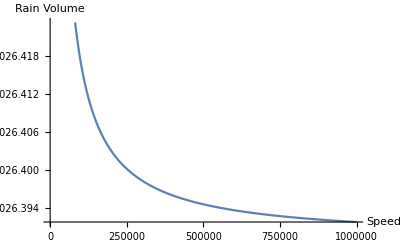

```mathematica
rainVolume[s_]:=(1000/s)*flux[s]
Plot[rainVolume[s],{s,0,1000000}, AxesLabel->{Speed,"Rain Volume"}]
```

9. Interpret the results from the problem above: As you increase your speed, does the volume of rain
hitting the windshield increase or decrease? If you drive REALLY fast, can you make the volume of
rain hitting the windshield arbitrarily small (since you are only in the rain for a really short time)? Or
is there a minimum volume of rain that will hit the windshield no matter how fast you drive? Does
this make sense? Why or why not?

Answer: As the car speed increases, the volume of rain hitting the windshield decreases. The volume of the rain decays in a form of the function f(x) = x^(-1/n) for n>0. As n grows larger, f(x) gets smaller; however it would never reach 0. So when the car drives “really fast” the volume of rain hitting the windshield gets smaller until a certain point, the minimum is around 1026.  This makes sense, because if the speed of the rain remains constant while the speed of the car is getting larger, the volume of rain that hits the car windshield would decrease but there’s always going to be some rain coming through...